```mathematica
(* srednice pizz - malej, sredniej i duzej *)
sm = 25;
ss = 31;
sd = 41;
rm = 1/2 sm;rs = 1/2 ss;rd=1/2 sd;

(* ceny pizz - malej, sredniej i duzej *)
cm =25.7;
cs = 28.5;
cd = 37.5;

ccmm = cm/(Pi*rm^2); ccms = cs/(Pi*rs^2);ccmd = cd/(Pi*rd^2);
```

```mathematica
(* ceny za centymetr kwadratowy (mniej - lepiej) *)
```

```mathematica
(* malej *) ccmm
```

0.0523556

```mathematica
(* sredniej *) ccms
```

0.03776

```mathematica
(* duzej *) ccmd
```

0.0284036

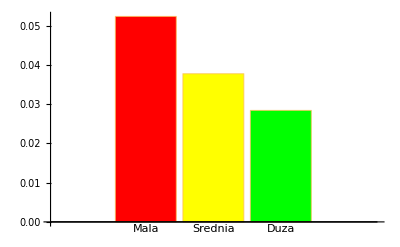

```mathematica
BarChart[{ccmm, ccms, ccmd}, ChartLabels->{"Mala", "Srednia", "Duza"}, ChartStyle->{Red, Yellow, Green, Yellow}, ChartLegends->"Cena za centymetr kwadratowy pizzy"]
```

```mathematica
(* Oplacalnosc - stosunki stosunkow
"Ile razy bardziej wieksza jest bardziej oplacalna od mniejszej"
 *)
```

```mathematica
(* Srednia od malej *) ccmm/ccms
```

1.38654

```mathematica
(* Duza od malej *)ccmm/ccmd
```

1.84327

```mathematica
(* Duza od sredniej *) ccms/ccmd
```

1.32941

```mathematica
(* Oplacalnosc - ile kosztowaloby tyle samo duzej pizzy kupując mniejsze pizze *)
```

```mathematica
(* kupując małe *)
```

```mathematica
ccmm * Pi * rd^2
```

69.1227

```mathematica
(* kupujac srednie *)
ccms * Pi * rd^2
```

49.8528

```mathematica
(* kupujac duze *)
ccmd * Pi *rd^2
```

37.5